```mathematica
string=NotebookDirectory[];
FileTensorAnalysis=string<>"TensorAnalysis.nb";
FileFuncao1=string<>"Funcao1.nb";
FileFuncao2=string<>"Funcao2.nb";
vecStrings={FileTensorAnalysis,FileFuncao1,FileFuncao2};
For[is=1,is≤Length[vecStrings],is++,
nb=NotebookOpen[vecStrings[[is]]];
SelectionMove[nb,All,Notebook];
SelectionEvaluate[nb];
NotebookClose[nb];
]
```

```mathematica
Function1[Log[A/C]/B/.exemple,0]
LFunction[EpsEqL[Log[A/C]/B/.exemple]]
```

-2.77556×10^-17

0.489305

```mathematica
ElastoPlasticL[L_,EP_,ETotal_]:=Block[{Lnext,θnext,EPnext,valf1,valf2,SigI1xJ2,SigTrial,EElast,EElastIJ,delL,I1next,J2next,lval,diffsig,diffsigIJ,sigresult,IJQuadrant,epsp,epsprev,epsmax,pr},
pr=True;
Lnext=L;
EElast=ETotal-EP;
EElastIJ=ToIJ[EElast];
IJQuadrant=EElastIJ[[3]];
SigI1xJ2={3 K EElastIJ[[1]],2G EElastIJ[[2]],IJQuadrant}/.exemple;
SigTrial=FromIJ[SigI1xJ2];
valf1=Function1[SigI1xJ2[[1]],SigI1xJ2[[2]]] // Chop;
valf2=Function2L[SigI1xJ2[[1]],SigI1xJ2[[2]],L]//Chop;
epsmax=2;
If[pr,
Print["ETotal = ",ETotal];
Print["SigI1xJ2 = ",SigI1xJ2];
Print["L ",L];
Print["valf1 = ",valf1];
Print["valf2 = ",valf2];
];
If[(valf2≤ 0 && SigI1xJ2[[1]] ≤  L) || (valf1 ≤ 0 && SigI1xJ2[[1]] ≥ L),
Print["Elastic"];
Lnext = L;
sigresult=FromIJ[SigI1xJ2];
EPnext=EP
,If[valf2 >0 && SigI1xJ2[[1]] ≤ L,
Print["Project F2"];
{θnext,delL}=NewtonFuncL[L,SigI1xJ2];
Lnext=L+delL;
lval=Lnext;
I1next=lval+F[lval]R Cos[θnext]/.exemple;
J2next=F[lval]Sin[θnext]/.exemple;
Print["Function2L = ",Function2L[I1next,J2next,Lnext]];
sigresult=FromIJ[{I1next,J2next,IJQuadrant}];
diffsig=FromIJ[SigI1xJ2]-FromIJ[{I1next,J2next,IJQuadrant}];
diffsigIJ=ToIJ[diffsig];
EPnext=EP+FromIJ[{diffsigIJ[[1]]/(3 K),diffsigIJ[[2]]/(2G),diffsigIJ[[3]]}]/.exemple;
,
Print["Project F1"];
I1next=NewtonF1[SigI1xJ2];
J2next = F[I1next]/.exemple;
If[J2next<0,
Print["Point is wasted J2next = ",J2next];
I1next=Log[A/C]/B/.exemple;
J2next = 0.;
epsmax=EpsEqL[I1next]/.exemple;
Print[" eps max ",epsmax];
];
Print["Function 1 I1next ",I1next," J2next ",J2next," value ",Function1[I1next,J2next]];
sigresult=FromIJ[{I1next,J2next,IJQuadrant}];
diffsig=FromIJ[SigI1xJ2]-sigresult;
diffsigIJ=ToIJ[diffsig];
EPnext=EP+FromIJ[{diffsigIJ[[1]]/(3K),diffsigIJ[[2]]/(2G),diffsigIJ[[3]]}]/.exemple;
epsprev = EpsEqL[L]/.exemple;
epsp=epsprev+diffsigIJ[[1]]/(3K)/.exemple;
If[epsp > epsmax,epsp=epsmax];
Lnext=LFunction[epsp]/.exemple;
Print["epsprev ",epsprev, " epspnext ",epsp," Lprev ",L," Lnext ",Lnext]; 
If[I1next<Lnext,Print["******* Should have projected onto F2 ***********"]];.08 
]
];
{Lnext,EPnext,sigresult,SigTrial}
]
locL=LFunction[0]
EP={0,0};

ETotal={0.05/3,0.0};
ElastoPlasticL[0,EP,ETotal]

ETotal={-0.065/50,0.0};
ElastoPlasticL[locL,EP,ETotal]
```

0.133045

ETotal = {0.0166667,0.}

SigI1xJ2 = {3.33333,0.7698,-1}

L 0

valf1 = 2.19937

valf2 = 482.749

Project F1

sigtrial {3.33333,0.7698,-1}

I1 start value 0.8

I1Val = 0.792513

F[I1] = -0.0561087

Diffval = 0.

Point is wasted J2next = -0.0561087

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.00730205 epspnext 0.00691309 Lprev 0 Lnext 0.24382

{0.24382,{0.0158495,-0.000817174},{0.163435,0.163435},{2.,0.666667}}

ETotal = {-0.0013,0.}

SigI1xJ2 = {-0.26,0.0600444,1}

L 0.133045

valf1 = -0.0387324

valf2 = 9.00047

Project F2

residue = {0.00595982,0.00286092}

residue = {-5.42791×10^-6,1.1447×10^-6}

residue = {2.20712×10^-13,4.55747×10^-13}

residue = {-4.44089×10^-16,1.11022×10^-15}

residue = {-4.44089×10^-16,-4.996×10^-16}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {4.44089×10^-16,1.05471×10^-15}

Function2L = -1.11022×10^-16

{0.111117,{-0.000838619,-0.000217913},{-0.0379327,0.0164108},{-0.156,-0.052}}

```mathematica
ListETotalL=Table[{epsa,0},{epsa,0,-0.06,-0.06/12}]
ListETotalL=Join[ListETotalL,Table[{epsa,0},{epsa,-0.06,-0.046,0.002}]]
ListETotalL=Join[ListETotalL,Table[{epsa,0},{epsa,-0.046,0.014,0.01}]]
(*ListETotalL=Join[ListETotalL,Reverse[ListETotalL]]*)
ResultL={{LFunction[0],{0,0},{0,0},{0,0}}};
test=ElastoPlasticL[ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL[[2]]]
ElastoPlasticL[test[[1]],test[[2]],ListETotalL[[2]]]

For[i=2,i<=Length[ListETotalL],i++,
AppendTo[ResultL,ElastoPlasticL[ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL[[i]]]]
]
ElastoPlasticL[ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL[[-1]]]
```

{{0.,0},{-0.005,0},{-0.01,0},{-0.015,0},{-0.02,0},{-0.025,0},{-0.03,0},{-0.035,0},{-0.04,0},{-0.045,0},{-0.05,0},{-0.055,0},{-0.06,0}}

{{0.,0},{-0.005,0},{-0.01,0},{-0.015,0},{-0.02,0},{-0.025,0},{-0.03,0},{-0.035,0},{-0.04,0},{-0.045,0},{-0.05,0},{-0.055,0},{-0.06,0},{-0.06,0},{-0.058,0},{-0.056,0},{-0.054,0},{-0.052,0},{-0.05,0},{-0.048,0},{-0.046,0}}

{{0.,0},{-0.005,0},{-0.01,0},{-0.015,0},{-0.02,0},{-0.025,0},{-0.03,0},{-0.035,0},{-0.04,0},{-0.045,0},{-0.05,0},{-0.055,0},{-0.06,0},{-0.06,0},{-0.058,0},{-0.056,0},{-0.054,0},{-0.052,0},{-0.05,0},{-0.048,0},{-0.046,0},{-0.046,0},{-0.036,0},{-0.026,0},{-0.016,0},{-0.006,0},{0.004,0},{0.014,0}}

ETotal = {-0.005,0}

SigI1xJ2 = {-1.,0.23094,1}

L 0.133045

valf1 = 0.0730477

valf2 = 90.3582

Project F2

residue = {-0.000353843,0.0410449}

residue = {3.02943×10^-6,0.00006721}

residue = {6.58584×10^-13,1.87922×10^-10}

residue = {4.44089×10^-16,-5.55112×10^-16}

residue = {0.,7.77156×10^-16}

residue = {0.,-5.55112×10^-16}

residue = {0.,7.77156×10^-16}

Function2L = 1.66533×10^-16

{0.0491183,{-0.00420853,-0.000257337},{-0.0743895,0.00951512},{-0.6,-0.2}}

ETotal = {-0.005,0}

SigI1xJ2 = {-0.0553593,0.0484424,1}

L 0.0491183

valf1 = -0.0281117

valf2 = 0

Elastic

{0.0491183,{-0.00420853,-0.000257337},{-0.0743895,0.00951512},{-0.0743895,0.00951512}}

ETotal = {-0.005,0}

SigI1xJ2 = {-1.,0.23094,1}

L 0.133045

valf1 = 0.0730477

valf2 = 90.3582

Project F2

residue = {-0.000353843,0.0410449}

residue = {3.02943×10^-6,0.00006721}

residue = {6.58584×10^-13,1.87922×10^-10}

residue = {4.44089×10^-16,-5.55112×10^-16}

residue = {0.,7.77156×10^-16}

residue = {0.,-5.55112×10^-16}

residue = {0.,7.77156×10^-16}

Function2L = 1.66533×10^-16

ETotal = {-0.01,0}

SigI1xJ2 = {-1.05536,0.279382,1}

L 0.0491183

valf1 = 0.118136

valf2 = 65.7538

Project F2

residue = {0.00159548,0.0395856}

residue = {1.02587×10^-6,0.0000692483}

residue = {6.32605×10^-12,2.0847×10^-10}

residue = {0.,-8.88178×10^-16}

residue = {0.,6.66134×10^-16}

residue = {0.,-8.88178×10^-16}

residue = {0.,6.66134×10^-16}

Function2L = -5.55112×10^-17

ETotal = {-0.015,0}

SigI1xJ2 = {-1.1458,0.292252,1}

L -0.0392458

valf1 = 0.125788

valf2 = 49.4546

Project F2

residue = {0.00139925,0.0412776}

residue = {1.89423×10^-6,0.0000797864}

residue = {8.86979×10^-12,2.96929×10^-10}

residue = {-4.44089×10^-16,1.33227×10^-15}

residue = {4.44089×10^-16,-4.44089×10^-16}

residue = {-4.44089×10^-16,-2.22045×10^-16}

residue = {4.44089×10^-16,-2.22045×10^-16}

Function2L = 1.11022×10^-16

ETotal = {-0.02,0}

SigI1xJ2 = {-1.25363,0.301907,1}

L -0.134408

valf1 = 0.129621

valf2 = 38.8843

Project F2

residue = {0.00157559,0.0436269}

residue = {2.69656×10^-6,0.0000953396}

residue = {1.50129×10^-11,4.54587×10^-10}

residue = {0.,6.66134×10^-16}

residue = {0.,6.66134×10^-16}

residue = {0.,6.66134×10^-16}

residue = {0.,-8.88178×10^-16}

Function2L = 1.66533×10^-16

ETotal = {-0.025,0}

SigI1xJ2 = {-1.37178,0.311395,1}

L -0.238294

valf1 = 0.133193

valf2 = 31.4465

Project F2

residue = {0.00185523,0.0463114}

residue = {3.82143×10^-6,0.000115513}

residue = {2.6827×10^-11,7.18419×10^-10}

residue = {0.,8.88178×10^-16}

residue = {0.,4.44089×10^-16}

residue = {0.,4.44089×10^-16}

residue = {0.,-8.88178×10^-16}

Function2L = 1.66533×10^-16

ETotal = {-0.03,0}

SigI1xJ2 = {-1.50047,0.321111,1}

L -0.35249

valf1 = 0.136979

valf2 = 25.986

Project F2

residue = {0.00222221,0.0493131}

residue = {5.51518×10^-6,0.000141542}

residue = {4.99658×10^-11,1.16745×10^-9}

residue = {0.,6.66134×10^-16}

residue = {0.,6.66134×10^-16}

residue = {0.,4.44089×10^-16}

residue = {0.,-1.55431×10^-15}

Function2L = -5.55112×10^-17

ETotal = {-0.035,0}

SigI1xJ2 = {-1.64122,0.331132,1}

L -0.478845

valf1 = 0.141072

valf2 = 21.8543

Project F2

residue = {0.0027015,0.0526665}

residue = {8.14565×10^-6,0.00017547}

residue = {9.72191×10^-11,1.95406×10^-9}

residue = {-4.44089×10^-16,4.44089×10^-16}

residue = {0.,2.22045×10^-16}

residue = {0.,2.22045×10^-16}

residue = {4.44089×10^-16,-1.33227×10^-15}

Function2L = 1.11022×10^-16

ETotal = {-0.04,0}

SigI1xJ2 = {-1.79612,0.341486,1}

L -0.619656

valf1 = 0.145517

valf2 = 18.6518

Project F2

residue = {0.00333747,0.0564161}

residue = {0.0000123498,0.000220257}

residue = {1.98545×10^-10,3.37784×10^-9}

residue = {0.,1.11022×10^-15}

residue = {0.,-4.44089×10^-16}

residue = {0.,1.11022×10^-15}

residue = {0.,-4.44089×10^-16}

Function2L = -1.66533×10^-16

ETotal = {-0.045,0}

SigI1xJ2 = {-1.96786,0.352198,1}

L -0.777844

valf1 = 0.150356

valf2 = 16.12

Project F2

residue = {0.00419832,0.0606063}

residue = {0.0000192788,0.000280143}

residue = {4.27912×10^-10,6.04736×10^-9}

residue = {4.44089×10^-16,1.77636×10^-15}

residue = {-4.44089×10^-16,-1.33227×10^-15}

residue = {4.44089×10^-16,1.77636×10^-15}

residue = {0.,-1.33227×10^-15}

Function2L = 1.66533×10^-16

ETotal = {-0.05,0}

SigI1xJ2 = {-2.15985,0.363293,1}

L -0.957167

valf1 = 0.155639

valf2 = 14.0854

Project F2

residue = {0.00538929,0.0652697}

residue = {0.0000310809,0.000361181}

residue = {9.78775×10^-10,1.12416×10^-8}

residue = {4.44089×10^-16,4.44089×10^-16}

residue = {0.,4.44089×10^-16}

residue = {0.,4.44089×10^-16}

residue = {0.,4.44089×10^-16}

Function2L = 0.

ETotal = {-0.055,0}

SigI1xJ2 = {-2.37651,0.374799,1}

L -1.16253

valf1 = 0.161422

valf2 = 12.4281

Project F2

residue = {0.00707516,0.0704057}

residue = {0.0000518802,0.000471847}

residue = {2.38803×10^-9,2.17329×10^-8}

residue = {0.,1.33227×10^-15}

residue = {4.44089×10^-16,-1.77636×10^-15}

residue = {0.,1.33227×10^-15}

residue = {4.44089×10^-16,1.33227×10^-15}

Function2L = 4.44089×10^-16

ETotal = {-0.06,0}

SigI1xJ2 = {-2.62358,0.38674,1}

L -1.40039

valf1 = 0.167776

valf2 = 11.0631

Project F2

residue = {0.00951633,0.0759371}

residue = {0.0000897483,0.000623427}

residue = {6.23214×10^-9,4.36639×10^-8}

residue = {-4.44089×10^-16,0.}

residue = {0.,0.}

residue = {0.,0.}

residue = {0.,0.}

Function2L = 1.38778×10^-16

ETotal = {-0.06,0}

SigI1xJ2 = {-1.90861,0.168195,1}

L -1.67934

valf1 = -0.0316969

valf2 = 0

Elastic

ETotal = {-0.058,0}

SigI1xJ2 = {-1.50861,0.0758187,1}

L -1.67934

valf1 = -0.108672

valf2 = -0.716284

Elastic

ETotal = {-0.056,0}

SigI1xJ2 = {-1.10861,0.0165573,-1}

L -1.67934

valf1 = -0.1478

valf2 = 0.427572

Elastic

ETotal = {-0.054,0}

SigI1xJ2 = {-0.70861,0.108933,-1}

L -1.67934

valf1 = -0.0291014

valf2 = 3.43157

Elastic

ETotal = {-0.052,0}

SigI1xJ2 = {-0.30861,0.201309,-1}

L -1.67934

valf1 = 0.0976868

valf2 = 8.2957

Project F1

sigtrial {-0.30861,0.201309,-1}

I1 start value -0.4

I1Val = -0.426325

F[I1] = 0.114724

Diffval = 2.22045×10^-16

Function 1 I1next -0.426325 J2next 0.114724 value 0.

epsprev -0.050457 epspnext -0.0498684 Lprev -1.67934 Lnext -1.62889

ETotal = {-0.05,0}

SigI1xJ2 = {-0.0263254,0.2071,-1}

L -1.62889

valf1 = 0.133953

valf2 = 11.6288

Project F1

sigtrial {-0.0263254,0.2071,-1}

I1 start value -0.2

I1Val = -0.205843

F[I1] = 0.0931889

Diffval = 0.

Function 1 I1next -0.205843 J2next 0.0931889 value 0.

epsprev -0.0498684 epspnext -0.0489708 Lprev -1.62889 Lnext -1.55567

ETotal = {-0.048,0}

SigI1xJ2 = {0.194157,0.185565,-1}

L -1.55567

valf1 = 0.140571

valf2 = 14.0709

Project F1

sigtrial {0.194157,0.185565,-1}

I1 start value -1.02696×10^-15

I1Val = -0.010994

F[I1] = 0.071321

Diffval = 1.11022×10^-16

Function 1 I1next -0.010994 J2next 0.071321 value 0.

epsprev -0.0489708 epspnext -0.047945 Lprev -1.55567 Lnext -1.47696

ETotal = {-0.046,0}

SigI1xJ2 = {0.389006,0.163697,-1}

L -1.47696

valf1 = 0.147293

valf2 = 16.4187

Project F1

sigtrial {0.389006,0.163697,-1}

I1 start value 0.2

I1Val = 0.159517

F[I1] = 0.0496966

Diffval = -1.11022×10^-16

Function 1 I1next 0.159517 J2next 0.0496966 value 0.

epsprev -0.047945 epspnext -0.0467976 Lprev -1.47696 Lnext -1.3945

ETotal = {-0.046,0}

SigI1xJ2 = {0.159517,0.0496966,-1}

L -1.3945

valf1 = 0

valf2 = 11.0978

Elastic

ETotal = {-0.036,0}

SigI1xJ2 = {2.15952,0.511577,-1}

L -1.3945

valf1 = 1.02654

valf2 = 70.0152

Project F1

sigtrial {2.15952,0.511577,-1}

I1 start value 0.7

I1Val = 0.650033

F[I1] = -0.0282386

Diffval = 0.

Point is wasted J2next = -0.0282386

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0467976 epspnext -0.0384515 Lprev -1.3945 Lnext -0.921711

ETotal = {-0.026,0}

SigI1xJ2 = {2.4903,0.46188,-1}

L -0.921711

valf1 = 1.16664

valf2 = 87.7638

Project F1

sigtrial {2.4903,0.46188,-1}

I1 start value 0.9

I1Val = 0.830604

F[I1] = -0.0640214

Diffval = 0.

Point is wasted J2next = -0.0640214

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0384515 epspnext -0.0284515 Lprev -0.921711 Lnext -0.531916

ETotal = {-0.016,0}

SigI1xJ2 = {2.4903,0.46188,-1}

L -0.531916

valf1 = 1.16664

valf2 = 107.984

Project F1

sigtrial {2.4903,0.46188,-1}

I1 start value 0.9

I1Val = 0.830604

F[I1] = -0.0640214

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0640214

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0284515 epspnext -0.0184515 Lprev -0.531916 Lnext -0.246025

ETotal = {-0.006,0}

SigI1xJ2 = {2.4903,0.46188,-1}

L -0.246025

valf1 = 1.16664

valf2 = 147.909

Project F1

sigtrial {2.4903,0.46188,-1}

I1 start value 0.9

I1Val = 0.830604

F[I1] = -0.0640214

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0640214

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.0184515 epspnext -0.00845152 Lprev -0.246025 Lnext -0.0227199

ETotal = {0.004,0}

SigI1xJ2 = {2.4903,0.46188,-1}

L -0.0227199

valf1 = 1.16664

valf2 = 230.422

Project F1

sigtrial {2.4903,0.46188,-1}

I1 start value 0.9

I1Val = 0.830604

F[I1] = -0.0640214

Diffval = -1.11022×10^-16

Point is wasted J2next = -0.0640214

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev -0.00845152 epspnext 0.00154848 Lprev -0.0227199 Lnext 0.159021

ETotal = {0.014,0}

SigI1xJ2 = {2.4903,0.46188,-1}

L 0.159021

valf1 = 1.16664

valf2 = 436.299

Project F1

sigtrial {2.4903,0.46188,-1}

I1 start value 0.9

I1Val = 0.830604

F[I1] = -0.0640214

Diffval = 1.11022×10^-16

Point is wasted J2next = -0.0640214

eps max 0.0256667

Function 1 I1next 0.490305 J2next 0. value -2.77556×10^-17

epsprev 0.00154848 epspnext 0.0115485 Lprev 0.159021 Lnext 0.311305

ETotal = {0.014,0}

SigI1xJ2 = {0.490305,3.20494×10^-16,1}

L 0.311305

valf1 = 0

valf2 = 5.42177

Elastic

{0.311305,{0.0131828,-0.000817174},{0.163435,0.163435},{0.163435,0.163435}}

```mathematica
(*ListETotalL2=Reverse[ListETotalL]
ResultL2={{ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL[[-1]]}}
test=ElastoPlasticL[ResultL[[-1,1]],ResultL[[-1,2]],ListETotalL2[[1]]]
ElastoPlasticL[test[[1]],test[[2]],ListETotalL2[[1]]]

For[i=2,i≤Length[ListETotalL2],i++,
AppendTo[ResultL2,ElastoPlasticL[ResultL2[[-1,1]],ResultL2[[-1,2]],ListETotalL2[[i]]]]
]
ElastoPlasticL[ResultL2[[-1,1]],ResultL2[[-1,2]],ListETotalL2[[-1]]]*)
```

```mathematica
(*ResultL2
ResultIJL2=Table[{ResultL2[[i,1]],ToIJ[ResultL2[[i,2]]],ToIJ[ResultL2[[i,3]]]},{i,Length[ResultL2]}]*)
```

```mathematica
ResultL
```

{{0.133045,{0,0},{0,0},{0,0}},{0.0491183,{-0.00420853,-0.000257337},{-0.0743895,0.00951512},{-0.6,-0.2}},{-0.0392458,{-0.00887203,-0.000199483},{-0.119397,-0.0132014},{-0.67439,-0.190485}},{-0.134408,{-0.013553,-0.0000894512},{-0.166488,-0.0435692},{-0.719397,-0.213201}},{-0.238294,{-0.0182191,0.0000390084},{-0.216829,-0.0774775},{-0.766488,-0.243569}},{-0.35249,{-0.0228644,0.000183361},{-0.270944,-0.114763},{-0.816829,-0.277478}},{-0.478845,{-0.0274852,0.000345622},{-0.32943,-0.155893},{-0.870944,-0.314763}},{-0.619656,{-0.0320775,0.000529074},{-0.393021,-0.20155},{-0.92943,-0.355893}},{-0.777844,{-0.0366367,0.000738},{-0.462637,-0.252612},{-0.993021,-0.40155}},{-0.957167,{-0.0411566,0.000977911},{-0.539446,-0.310204},{-1.06264,-0.452612}},{-1.16253,{-0.0456294,0.00125597},{-0.624949,-0.375779},{-1.13945,-0.510204}},{-1.40039,{-0.0500453,0.00158157},{-0.721093,-0.451241},{-1.22495,-0.575779}},{-1.67934,{-0.0543913,0.00196718},{-0.830418,-0.539096},{-1.32109,-0.651241}},{-1.67934,{-0.0543913,0.00196718},{-0.830418,-0.539096},{-0.830418,-0.539096}},{-1.67934,{-0.0543913,0.00196718},{-0.590418,-0.459096},{-0.590418,-0.459096}},{-1.67934,{-0.0543913,0.00196718},{-0.350418,-0.379096},{-0.350418,-0.379096}},{-1.67934,{-0.0543913,0.00196718},{-0.110418,-0.299096},{-0.110418,-0.299096}},{-1.62889,{-0.0529454,0.00153849},{-0.00963687,-0.208344},{0.129582,-0.219096}},{-1.55567,{-0.051002,0.00101561},{0.0389908,-0.122417},{0.230363,-0.128344}},{-1.47696,{-0.0490111,0.000533038},{0.0786897,-0.0448419},{0.278991,-0.0424171}},{-1.3945,{-0.0469832,0.0000927918},{0.110557,0.0244801},{0.31869,0.0351581}},{-1.3945,{-0.0469832,0.0000927918},{0.110557,0.0244801},{0.110557,0.0244801}},{-0.921711,{-0.0368172,-0.000817174},{0.163435,0.163435},{1.31056,0.42448}},{-0.531916,{-0.0268172,-0.000817174},{0.163435,0.163435},{1.36343,0.563435}},{-0.246025,{-0.0168172,-0.000817174},{0.163435,0.163435},{1.36343,0.563435}},{-0.0227199,{-0.00681717,-0.000817174},{0.163435,0.163435},{1.36343,0.563435}},{0.159021,{0.00318283,-0.000817174},{0.163435,0.163435},{1.36343,0.563435}},{0.311305,{0.0131828,-0.000817174},{0.163435,0.163435},{1.36343,0.563435}}}

```mathematica
ResultIJL=Table[{ResultL[[i,1]],ToIJ[ResultL[[i,2]]],ToIJ[ResultL[[i,3]]],ToIJ[ResultL[[i,4]]]},{i,Length[ResultL]}]
```

{{0.133045,{0,0,1},{0,0,1},{0,0,1}},{0.0491183,{-0.0047232,0.00228122,1},{-0.0553593,0.0484424,1},{-1.,0.23094,1}},{-0.0392458,{-0.009271,0.0050071,1},{-0.1458,0.0613123,1},{-1.05536,0.279382,1}},{-0.134408,{-0.0137319,0.00777316,1},{-0.253627,0.0709673,1},{-1.1458,0.292252,1}},{-0.238294,{-0.0181411,0.0105413,1},{-0.371784,0.0804547,1},{-1.25363,0.301907,1}},{-0.35249,{-0.0224977,0.0133066,1},{-0.50047,0.0901713,1},{-1.37178,0.311395,1}},{-0.478845,{-0.0267939,0.0160681,1},{-0.641215,0.100192,1},{-1.50047,0.321111,1}},{-0.619656,{-0.0310194,0.0188254,1},{-0.796121,0.110546,1},{-1.64122,0.331132,1}},{-0.777844,{-0.0351607,0.0215783,1},{-0.967861,0.121258,1},{-1.79612,0.341486,1}},{-0.957167,{-0.0392007,0.0243263,1},{-1.15985,0.132353,1},{-1.96786,0.352198,1}},{-1.16253,{-0.0431175,0.0270693,1},{-1.37651,0.143859,1},{-2.15985,0.363293,1}},{-1.40039,{-0.0468821,0.0298068,1},{-1.62358,0.155799,1},{-2.37651,0.374799,1}},{-1.67934,{-0.050457,0.0325386,1},{-1.90861,0.168195,1},{-2.62358,0.38674,1}},{-1.67934,{-0.050457,0.0325386,1},{-1.90861,0.168195,1},{-1.90861,0.168195,1}},{-1.67934,{-0.050457,0.0325386,1},{-1.50861,0.0758187,1},{-1.50861,0.0758187,1}},{-1.67934,{-0.050457,0.0325386,1},{-1.10861,0.0165573,-1},{-1.10861,0.0165573,-1}},{-1.67934,{-0.050457,0.0325386,1},{-0.70861,0.108933,-1},{-0.70861,0.108933,-1}},{-1.62889,{-0.0498684,0.0314563,1},{-0.426325,0.114724,-1},{-0.30861,0.201309,-1}},{-1.55567,{-0.0489708,0.0300324,1},{-0.205843,0.0931889,-1},{-0.0263254,0.2071,-1}},{-1.47696,{-0.047945,0.0286043,1},{-0.010994,0.071321,-1},{0.194157,0.185565,-1}},{-1.3945,{-0.0467976,0.0271793,1},{0.159517,0.0496966,-1},{0.389006,0.163697,-1}},{-1.3945,{-0.0467976,0.0271793,1},{0.159517,0.0496966,-1},{0.159517,0.0496966,-1}},{-0.921711,{-0.0384515,0.0207846,1},{0.490305,0.,1},{2.15952,0.511577,-1}},{-0.531916,{-0.0284515,0.0150111,1},{0.490305,0.,1},{2.4903,0.46188,-1}},{-0.246025,{-0.0184515,0.0092376,1},{0.490305,0.,1},{2.4903,0.46188,-1}},{-0.0227199,{-0.00845152,0.0034641,1},{0.490305,0.,1},{2.4903,0.46188,-1}},{0.159021,{0.00154848,0.0023094,-1},{0.490305,0.,1},{2.4903,0.46188,-1}},{0.311305,{0.0115485,0.0080829,-1},{0.490305,0.,1},{2.4903,0.46188,-1}}}

{0.133045,0.0491183,-0.0392458,-0.134408,-0.238294,-0.35249,-0.478845,-0.619656,-0.777844,-0.957167,-1.16253,-1.40039,-1.67934,-1.67934,-1.67934,-1.67934,-1.67934,-1.62889,-1.55567,-1.47696,-1.3945,-1.3945,-0.921711,-0.531916,-0.246025,-0.0227199,0.159021,0.311305}

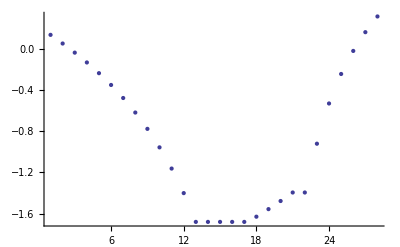

```mathematica
val=Table[ResultL[[i,1]],{i,Length[ResultL]}]
ListPlot[val]
ClearAll[val]
```

```mathematica
Length[ListETotalL]
Length[ResultIJL]
```

28

28

```mathematica
(*DeformElastL2=Table[ToIJ[ListETotalL2[[i]]-FromIJ[ResultIJL2[[i,2]]]],{i,1,Length[ResultL2]}];
SigElastIJL2=Table[{K DeformElastL2[[i,1]],2 G DeformElastL2[[i,2]],DeformElastL2[[i,3]]}/.exemple,{i,1,Length[ResultL2]}];
SigElastIJLplot=Table[{K DeformElastL2[[i,1]],2 G DeformElastL2[[i,2]]}/.exemple,{i,1,Length[ResultL2]}];
gl=ListPlot[SigElastIJLplot]
Show[gl,bg]
Diff=Table[SigElastIJL2[[i]]-ResultIJL2[[i,3]],{i,1,Length[ResultL2]}]//Chop
Table[Function1[ResultIJL2[[i,3,1]],ResultIJL2[[i,3,2]]],{i,1,Length[ResultL2]}]*)
```

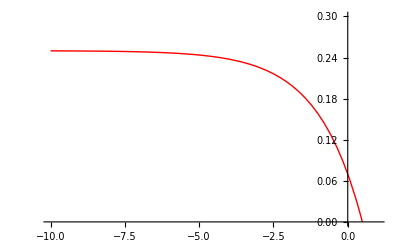

```mathematica
bg
```

```mathematica
ResultIJL[[2,4]]
ToIJ[ListETotalL[[2]]]
FromIJ[ResultIJL[[2,2]]]
ToIJ[ListETotalL[[2]]-FromIJ[ResultIJL[[2,2]]]]
```

{-1.,0.23094,1}

{-0.005,0.00288675,1}

{-0.00420853,-0.000257337}

{-0.000276797,0.00060553,1}

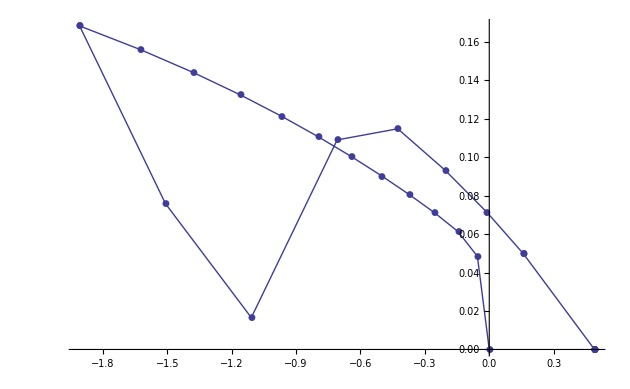

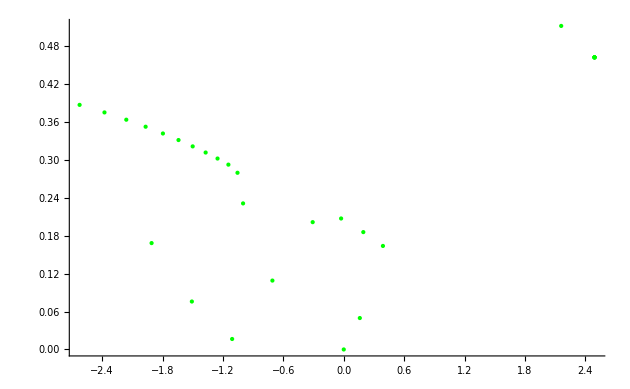

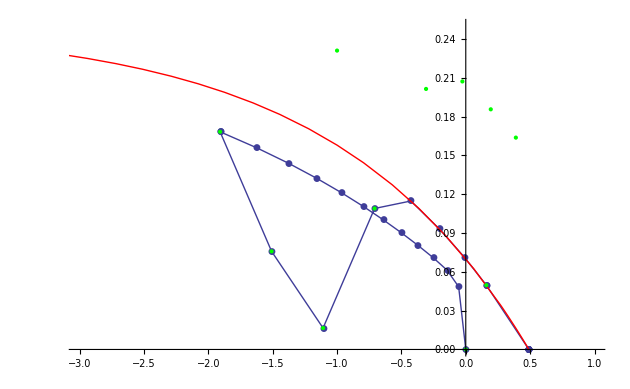

{{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,-2},{0,0,0},{0,0,0},{0,0,0},{0,0,0},{0,0,0}}

{-0.07,-0.0281117,-0.0254396,-0.0271624,-0.0292343,-0.0311083,-0.0326716,-0.0338653,-0.0346299,-0.0348942,-0.0345699,-0.033548,-0.0316969,-0.0316969,-0.108672,-0.1478,-0.0291014,5.55112×10^-17,0.,0.,2.77556×10^-17,-4.16334×10^-16,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17,-2.77556×10^-17}

```mathematica
DeformElastL=Table[ToIJ[ListETotalL[[i]]-FromIJ[ResultIJL[[i,2]]]],{i,1,Length[ListETotalL]}];
SigElastIJL=Table[{3K DeformElastL[[i,1]],2 G DeformElastL[[i,2]],DeformElastL[[i,3]]}/.exemple,{i,1,Length[ListETotalL]}];
SigElastIJL2=Table[{3K DeformElastL[[i,1]],2 G DeformElastL[[i,2]]}/.exemple,{i,1,Length[ListETotalL]}];
SigTrialIJL=Table[{ResultIJL[[i,4,1]],ResultIJL[[i,4,2]]},{i,Length[ResultIJL]}];
gl=ListPlot[SigElastIJL2,PlotJoined->True,PlotMarkers->Automatic]
gl2=ListPlot[SigTrialIJL,PlotStyle->{Green}]
Show[gl,bg,gl2,PlotRange->{{-3,1},{0,0.25}}]
Diff=Table[SigElastIJL[[i]]-ResultIJL[[i,3]],{i,1,Length[ListETotalL]}]//Chop
Table[Function1[ResultIJL[[i,3,1]],ResultIJL[[i,3,2]]],{i,1,Length[ListETotalL]}]
```

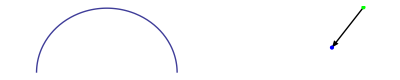

```mathematica
ShowPoint[i_]:=Block[{frompoint,topoint,arrow,dot1,dot2,ellips},
frompoint={ResultIJL[[i,4,1]],ResultIJL[[i,4,2]]};
topoint={ResultIJL[[i,3,1]],ResultIJL[[i,3,2]]};
arrow=Graphics[{Arrowheads[0.02],Arrow[{frompoint,topoint}]}];
dot1=Graphics[{PointSize[Large],Green,Point[frompoint]}];
dot2=Graphics[{PointSize[Large],Blue,Point[topoint]}];
ellips=Ag[ResultL[[i,1]]];
{arrow,dot1,dot2,ellips}
]
Show[ShowPoint[20]]
```

```mathematica
Animate[Show[ShowPoint[i],PlotRange->{{-3,2},{-0.1,0.4}}],{i,1,Length[ResultIJL],1},AnimationRunning->False]
```

```mathematica
Animate[Show[gl,bg,gl2,ShowPoint[i],PlotRange->{{-3,1},{0,0.25}}],{i,1,Length[ResultIJL],1},AnimationRunning->False]
```

```mathematica
TableShowPoint=Table[Show[gl,bg,gl2,ShowPoint[i],PlotRange->{{-3,1},{0,0.25}}],{i,1,Length[ResultIJL]}];
string=NotebookDirectory[];
FileAnimationL=string<>"AnimationL.gif";
Export[FileAnimationL,TableShowPoint]
```

/Users/phil/Dropbox/Projeto_LabMec_2011_14/Plasticidade/Aprendizado/AnimationL.gif

{{0.,0},{-0.005,-0.0743895},{-0.01,-0.119397},{-0.015,-0.166488},{-0.02,-0.216829},{-0.025,-0.270944},{-0.03,-0.32943},{-0.035,-0.393021},{-0.04,-0.462637},{-0.045,-0.539446},{-0.05,-0.624949},{-0.055,-0.721093},{-0.06,-0.830418},{-0.06,-0.830418},{-0.058,-0.590418},{-0.056,-0.350418},{-0.054,-0.110418},{-0.052,-0.00963687},{-0.05,0.0389908},{-0.048,0.0786897},{-0.046,0.110557},{-0.046,0.110557},{-0.036,0.163435},{-0.026,0.163435},{-0.016,0.163435},{-0.006,0.163435},{0.004,0.163435},{0.014,0.163435}}

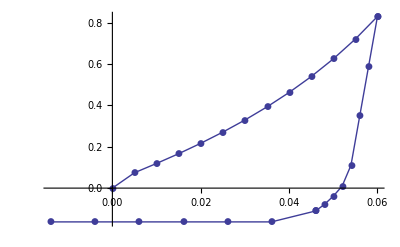

```mathematica
a=Table[{ListETotalL[[i,1]],ResultL[[i,3,1]]},{i,1,Length[ListETotalL]}]
ga=ListPlot[-a,PlotJoined->True,PlotMarkers->Automatic]
Clear[a,b,ga,gb]
```

```mathematica
a=Derivatives[Result[[1,3]],Result[[2,3]]-Result[[1,3]],Result[[1,1]]];
{{a[[1,1]]Sqrt[3],a[[1,2]]},{a[[2,1]]Sqrt[3],a[[2,2]]},a[[3]]}
{ListETotal[[2]],Result[[2,2]],Result[[2,1]]}
```

lval = 0.133045

flval = 0.0532179

gradf2 = {-26.0371,0.}

derivT = {-0.00191967,0.0157458}

dlval = 17.0081

B lval = 0.08914

- C B E^(B lval) = -0.131844

dfval = -2.24242

one = 255.675

two = 84.2732

three = 0.

four = 0.

df2depsp = 339.949

epspponto = -0.00014703

trN2 = -45.0976

gammaponto = 3.26026×10^-6

deformPlast = {-0.0000848878,0.}

ST = {0,1}

deformElast = {-0.0000166248,0.000196822}

{{-0.000175825,0.000196822},{-0.00014703,0.},-0.00014703}

{{-0.000325,0.000187639},{-0.000275126,0.0000484644},-0.000275126}

```mathematica
ElastoPlastic[Result[[1,1]],Result[[1,2]],ListETotal[[2]]]
```

ETotal = {-0.000325,0.000187639}

SigI1xJ2 = {-0.0216667,0.0150111}

valf2 = 0.431788

subit {I1T→-0.0216667,J2T→0.0150111}

θ = -π

θ = -(19 π)/20

θ = -(9 π)/10

θ = -(17 π)/20

θ = -(4 π)/5

θ = -(3 π)/4

θ = -(7 π)/10

θ = -(13 π)/20

θ = -(3 π)/5

θ = -(11 π)/20

θ = -π/2

θ = -(9 π)/20

θ = -(2 π)/5

θ = -(7 π)/20

θ = -(3 π)/10

θ = -π/4

θ = -π/5

θ = -(3 π)/20

θ = -π/10

θ = -π/20

θ = 0

θ = π/20

θ = π/10

θ = (3 π)/20

θ = π/5

θ = π/4

θ = (3 π)/10

θ = (7 π)/20

θ = (2 π)/5

θ = (9 π)/20

θ = π/2

θ = (11 π)/20

θ = (3 π)/5

θ = (13 π)/20

θ = (7 π)/10

θ = (3 π)/4

θ = (4 π)/5

θ = (17 π)/20

θ = (9 π)/10

θ = (19 π)/20

θ = π

restheta = {5.67729,5.34003,5.12872,4.9867,4.87787,4.78283,4.69152,4.5989,4.5027,4.4021,4.29704,4.18782,4.07487,3.9587,3.83975,3.71847,3.59526,3.47045,3.34437,3.21729,3.08947,2.96115,3.45065,3.57936,3.70797,3.83632,3.96425,4.09163,4.21839,4.34455,4.47028,4.59604,4.72284,4.85265,4.98938,5.14073,5.32211,5.56417,5.91817,0.122311,0.605891}

θ = (19 π)/20

θ = (19 π)/20

residue = {0.122311,0.00034957}

tangent = {{3.32067,-242.53},{-0.000312192,1.33818}}

delu = {0.0568818,0.000274499}

θ = 2.92763

delepsp = -0.000274499

θ = 2.92763

residue = {-0.0229419,3.22682×10^-6}

tangent = {{4.02657,-202.504},{-0.000428652,1.33871}}

delu = {-0.00566767,5.95617×10^-7}

θ = 2.9333

delepsp = -0.000275094

θ = 2.9333

residue = {0.0000914666,3.16371×10^-8}

tangent = {{4.05591,-225.014},{-0.000417475,1.33881}}

delu = {0.0000242825,3.12026×10^-8}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {-1.41228×10^-9,5.93007×10^-13}

tangent = {{4.05592,-224.935},{-0.000417523,1.33881}}

delu = {-3.29334×10^-10,3.40229×10^-13}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {0.,1.6263×10^-19}

tangent = {{4.05592,-224.935},{-0.000417523,1.33881}}

delu = {6.85528×10^-18,1.23612×10^-19}

θ = 2.93327

delepsp = -0.000275126

θ = 2.93327

residue = {0.,5.42101×10^-20}

Function2 = 2.22045×10^-16

{-0.000275126,{-0.000275126,0.0000484644},{-0.00332496,0.011134}}

```mathematica
{K,2G}/.exemple
{ListETotal[[2,1]]K,ListETotal[[2,2]]2G}/.exemple
(%-Result[[2,3]])/.exemple
{%[[1]]/K,%[[2]]/(2G)}/.exemple
```

{66.6667,80}

{-0.216667,0.150111}

{-0.179007,0.117562}

{-0.0026851,0.00146953}

```mathematica
Result[[2]]
```

{-0.000275126,{-0.000275126,0.0000484644},{-0.00332496,0.011134}}

```mathematica
epsp=Result[[2,1]]
theta=2.5604883056356527;
l=LFunction[epsp];
fl=F[l]/.exemple;
i1theta=l+fl R Cos[theta]/.exemple;
i1=Result[[2,3,1]];
i1-i1theta;
sqj2=Result[[2,3,2]];
sqj2theta=fl Sin[theta];
sqj2theta-sqj2;
(l-i1)^2 /(fl R)^2 + sqj2^2/fl^2 -1/.exemple;
gfv1=2√3(i1-l)/(fl R)^2/.exemple;
√3 gfv1;
gfv2=√2 sqj2/fl^2;
sqj2/fl;
ep=Result[[2,2]];
ArcTan[ep[[1]],ep[[2]]]
epprop={6(i1-l)/(fl R)^2,(2sqj2)/fl^2}/.exemple
ArcTan[epprop[[1]],epprop[[2]]]
TmTt={K epprop[[1]],2G epprop[[2]]}/.exemple
sigtrial={ListETotal[[2,1]]K,ListETotal[[2,2]]2G}/.exemple;
sigma=Result[[2,3]]
difsigma=(sigtrial-sigma)/.exemple;
ArcTan[difsigma[[1]],difsigma[[2]]]
ep-{difsigma[[1]]/K,difsigma[[2]]/(2G)}/.exemple
ArcTan[TmTt[[1]],TmTt[[2]]]
ArcTan[2 G R difsigma[[1]],3K difsigma[[2]]]/.exemple
theta
difsigma

Print[" delta gamma ",δγ2=epsp/epprop[[1]]]
Tepprop={K epprop[[1]],2G epprop[[2]]}/.exemple;
toto=Tepprop δγ2
ArcTan[difsigma[[1]],difsigma[[2]]]
ArcTan[toto[[1]],toto[[2]]]
δγ2 epprop-ep


Print["Checking stress functions"];
sigma
sqj2
l
fl
Print["gradf ",{epprop[[1]]/Sqrt[3],epprop[[2]]/Sqrt[2]}]
{sigma[[1]]/Sqrt[3],sigma[[2]]Sqrt[2]}

DLFunction[epsp]
B l/.exemple
dF[l]/.exemple
DLFunction[epsp]dF[l]/.exemple
a=DLFunction[epsp](2(l-i1))/(fl R)^2/.exemple
b=DLFunction[epsp](-(2(l-i1)^2)/(fl^3 R^2)dF[l])/.exemple
c=DLFunction[epsp](-(2sigma[[2]]^2)/fl^3 dF[l])/.exemple
Print["four ",DLFunction[epsp](-(2sigma[[2]]^2)/1 dF[l])/.exemple]
dfedep=DLFunction[epsp]((2(l-i1))/(fl R)^2-(2(l-i1)^2)/(fl^3 R^2)dF[l]-(2sqj2^2)/fl^3 dF[l])/.exemple
gradFT=epprop[[1]] sigma[[1]]/3+epprop[[2]] sigma[[2]]
(*Function2[sigma[[1]],sigma[[2]],epsp]-Function2[0,0,epsp]
Function2[sigma[[1]],sigma[[2]],0]-Function2[0,0,0]
*)
Print["epponto " ,a=epponto=-gradFT/dfedep]
Print["TrN2 ",epprop[[1]]]
Print["gammaponto ",gammaponto=epponto/epprop[[1]]]

epsp=0;
i1=0;
sqj2=0;
epprop={6(i1-l)/(fl R)^2,(2sqj2)/fl^2}/.exemple;
dfedep=DLFunction[epsp]((2(l-i1))/(fl R)^2-(2(l-i1)^2)/(fl^3 R^2)dF[l]-(2sqj2^2)/fl^3 dF[l])/.exemple
gradFT=epprop[[1]] sigma[[1]]/3+epprop[[2]] sigma[[2]]
(*Function2[sigma[[1]],sigma[[2]],epsp]-Function2[0,0,epsp]
Function2[sigma[[1]],sigma[[2]],0]-Function2[0,0,0]
*)
Print["epponto " ,b=epponto=-gradFT/dfedep]
Print["epponto medio ",(a+b)/2]
Print["TrN2 ",epprop[[1]]]
Print["gammaponto ",gammaponto=epponto/epprop[[1]]]


ClearAll[l,fl,i1,sqj2,gfv1,gfv2,epsp,theta,i1theta,sqj2theta,ep,epprop,TmTt,sigtrial,sigma,difsigma,Tepprop,toto,δγ2,dfedep,gradFT,epponto,a,b,c,gammaponto]
```

-0.000275126

2.96723

{-43.6165,7.68321}

2.96723

{-2907.77,614.657}

{-0.00332496,0.011134}

2.93327

{0.,0.}

2.93327

2.93327

2.56049

{-0.0183417,0.00387715}

delta gamma 6.30783×10^-6

{-0.0183417,0.00387715}

2.93327

2.93327

{5.42101×10^-20,-4.06576×10^-20}

Checking stress functions

{-0.00332496,0.011134}

0.011134

0.128354

0.0538354

gradf {-25.182,5.43285}

{-0.00191967,0.0157458}

17.0926

0.0859971

-0.13143

-2.24649

248.507

79.888

3.56967

four 0.000556972

331.965

0.133886

epponto -0.000403313

TrN2 -43.6165

gammaponto 9.2468×10^-6

316.564

0.0471204

epponto -0.00014885

epponto medio -0.000276081

TrN2 -42.5151

gammaponto 3.5011×10^-6

```mathematica
K
```

K